```mathematica
(* QuantumComputing`
   Jacob Austin Marks
  Wolfram Research
*)
```

```mathematica
BeginPackage["QuantumComputing`"];
```

## Usage Messages

```mathematica
QuantumDiscreteState::usage  = 
		"QuantumDiscreteState[w → {c_0, c_1, ..., c_n}] yields for quantum entity w"<>
		" the quantum state c_0'0 + c_1'1 + ... c_n'n, where c_i' are the normalized"<>
		" coefficients corresponding to c_i, and k is the k^th computational basis states.\n"<>
		
		"QuantumDiscreteState[{w_1, w_2} -> C] yields for (potentially entangled) quantum "<>
		"entities w_1 and w_2 the normalized quantum state ∑_(i,j)  C_(i,j)i,j"<>
		" where i ranges from 0 to d_1-1 and j ranges from 0 to d_2-1, "<>
		" with d_k being the dimension of wire k.\n"<>
		
		"QuantumDiscreteState[{w_1 → d_1, ..., w_n → d_n} → {\"BasisState\", {l_1, ..., l_n}}] yields the"<>
		" computational basis state l_1, ..., l_n for quantum entities w_i with dimensions d_i."<>
		" If no dimension is specified for w_i, then d_i = 2.\n"<>
		
		"QuantumDiscreteState[w -> \"Plus\"] yields the state + = (0 + 1)/(√2). "<>
		"\"Minus\" yields (0 - 1)/(√2).\n"<>
		
		"QuantumDiscreteState[{w_1, w_2} -> \"PhiPlus\"] yields for Φ_+ Bell State for "<>
		"quantum entities w_1 and w_2. The same format holds for Φ_-, Ψ_+, and Ψ_-.\n"<>
		
		"QuantumDiscreteState[{w_1, w_2, ..., w_n} → \"GHZ\"] yields an entangled GHZ state for "<>
		"quantum entities w_1, w_2, ..., w_n.\n"<>
		
		"QuantumDiscreteState[{w_1, w_2, ..., w_n} → \"W\"] yields an entangled W state for "<>
		"quantum entities w_1, w_2, ..., w_n.\n"<>
		
		"QuantumDiscreteState[{ws_1 → spec_1, ws_2 → spec_2, ..., ws_n → spec_n}] yields the tensor product state of"<>
		" the states corresponding to spec_1, ..., spec_n.\n"<>
		
		"QuantumDiscreteState[\"Mixture\", <|{state_1 → p_1, ..., state_n → p_n}|>] yields the mixed state"<>
		" with probability p_i of being in state_i.\n"<>
		
		"QuantumDiscreteState[\"Mixture\", (states → probs)] yields the mixed state"<>
		" with probability p_i of being in state_i.\n"<>
			
		"QuantumDiscreteState[\"Product\", {state_1, ..., state_n}] yields the tensor product state"<>
		" of QuantumStates state_1, ..., state_n ordered by the states' wire names.\n"<>
		
		"QuantumDiscreteState[\"Trace\", {qstate, wires}] yields the reduced state of qstate after"<>
		" tracing out wires."<>
		
		"QuantumDiscreteState[...][\"Purity\"] yields the purity of the "<>
		"quantum state, defined as Tr[ρ.ρ], where ρ is qstate's density matrix."<>
		
		"QuantumDiscreteState[...][\"VonNeumannEntropy\"] yields the Von Neumann Entropy of the "<>
		"quantum state, - ∑_j η_j Log_2η_j, where η_j are the eigenvalues of qstate.";
```

```mathematica
QuantumDiscreteStateQ::usage = "QuantumDiscreteStateQ[qs] yields true if qs is a valid QuantumDiscreteState"<>
	" and false otherwise.";
```

```mathematica
QuantumDiscreteOperation::usage = "QuantumDiscreteOperation[U, {w_1, w_2, ...}] yields the quantum operation"<>
	" of the unitary matrix U on {w_1, w_2, ...}.\n"<>
	
	"QuantumDiscreteOperation[\"Gate\", {w_1, w_2, ...}] yields the quantum operation specified by \"Gate\""<>
	" on w_1, w_2, ... Possible gates include CNOT, Hadamard, S, T, Fourier, PauliYGate, SWAP, Toffoli, etc..\n"<>
	
	"QuantumDiscreteOperation[\"PauliXGate\", {w}, \"QuditDimension\" -> D, \"Power\" -> k] yields the k^th power of"<>
	" of PauliX in the qudit stabilizer group of dimension D. PauliZGate, and Fourier"<>
	"  follow the same syntax.\n"<>
	
	"QuantumDiscreteOperation[{\"Rz\", θ} -> {w}] yields the operator representing a rotation of θ degrees"<>
	" about the Z-axis. Rx, Ry, and Deutsch (deutsch's gate) follow the same syntax.\n"<>
	
	"QuantumDiscreteOperation[...][qstate] yields the quantum state resulting from"<>
	" the action of the quantum operation on qstate.\n"<>
	
	"QuantumDiscreteOperation[{w_1, w_2} → {\"Control\", U}, \"QuditDimension\" -> d] yields the Controlled-unitary operation"<>
	" with w_1 as control and unitary matrix U acting on w_2 when w_1 takes on the value d.\n"<>
	
	"QuantumDiscreteOperation[{cond1 → op1, cond2 → op2, ...}, ws][qmeas] yields op_i, where cond_i is"<>
	" the first condition satisfied by the result value from RandomVariate[qmeas, 1]. If no conditions are satisfied"<>
	" or no measurement directly precedes this, op_1 is chosen.";
```

```mathematica
QuantumDiscreteConditionalOperation::usage = 
	"QuantumDiscreteConditionalOperation[{cond1 → op1, cond2 → op2, ...}, ws][qmeas] yields op_i, where cond_i is"<>
	" the first condition satisfied by the result value from RandomVariate[qmeas, 1]. If no conditions are satisfied"<>
	" or no measurement directly precedes this, op_1 is chosen.";
```

```mathematica
QuantumDiscreteOperationQ::usage = "QuantumDiscreteOperationQ[qop] yields true if qop is a valid"<>
	" QuantumDiscreteOperation and false otherwise.";
```

```mathematica
QuantumDiscreteConditionalOperationQ::usage = "QuantumDiscreteConditionalOperationQ[qop] yields true if qop is a valid"<>
	" QuantumDiscreteOperation and false otherwise.";
```

```mathematica
QuantumDiscreteMeasurement::usage = "QuantumDiscreteMeasurement[ws, qstate] yields the unevaluated measurement of "<>
	"wires w of QuantumDiscreteState qstate in the computational basis.\n"<>

	"QuantumDiscreteMeasurement[{w_1, w_2, ...} → povm, qstate] yields the unevaluated measurement of wires"<>
	" w_1, w_2, ... of QuantumDiscreteState qstate where the measurement operators are described by a QuantumDiscretePOVM povm.\n"<>

	"QuantumDiscreteMeasurement[{ws_1 → obs_1, ws_2 → obs_2, ...}, qstate] yields the unevaluated measurement on "<>
	"QuantumDiscreteState state ws_1, ws_2, ... of state qstate where the measurements results are "<>
	"projections of the state onto eigenvectors of obs_1, obs_2, ... QuantumDiscreteObservables. \n"<>

	"QuantumDiscreteMeasurement[specs, qstate][\"ProbabilityDistribution\"] yields an association "<>
	"<| state_i → prob_i|> containing the potential outcomes of the measurement and their probabilities.\n"<>
	
	"QuantumDiscreteMeasurement[specs, qstate][\"Collapse\"] collapses qstate down to state_i with "<>
	"probability prob_i from the measurement's probability distribution.";
```

```mathematica
QuantumDiscreteObservable::usage = "QuantumDiscreteObservable[desc] represents the observable corresponding "<>
	"to the Hermitean matrix desc.";
```

```mathematica
QuantumDiscreteObservableQ::usage = "QuantumDiscreteObservableQ[obs] yields true if obs is a valid"<>
	" QuantumDiscreteObservable and false otherwise.";
```

```mathematica
QuantumDiscretePOVM::usage = "QuantumDiscretePOVMQ[{M_1, M_2, ...}] represents the "<>
	"Positive Operator Valued Measure given by F_i = M_i^†M_i, where ∑_i F_i = 𝟙";
```

```mathematica
QuantumDiscretePOVMQ::usage = "QuantumDiscretePOVMQ[desc] yields true if desc forms a valid"<>
	" QuantumDiscretePOVM and false otherwise.";
```

```mathematica
QuantumCircuit::usage = "QuantumCircuit[{qop_1, qop_2,..., qop_n}] yields the quantum circuit"<>
		" which composes the quantum operations qop_1, qop_2,..., qop_n.\n"<>
		
		(* Have not implemented yet!!! *)		
		"QuantumCircuit[bf] yields a quantum circuit representation of the boolean function"<>
		" bf, expressed in terms of the fault-tolerant Clifford + T gate set.\n"<>
		
		"QuantumCircuit[{qcirc_1, qcirc_2,..., qcirc_n}] yields the concatenation of"<>
		" quantum circuits qcirc_1, qcirc_2,..., qcirc_n.\n"<>
		
		"QuantumCircuit[opsA] + QuantumCircuit[opsB] yields"<>
		" QuantumCircuit[Join[opsA, opsB]].\n"<>
		
		"QuantumCircuit[ops]^n yields QuantumCircuit[Flatten[ConstantArray[ops, n]]].\n"<>
		
		"QuantumCircuit[..., \"Simplify\" → \"True\"] yields the quantum circuit with"<>
		" all internal simplification rules applied. Other option values include"<>
		" \"False\", \"Paulis\", \"CNOTs\", and user-defined rules.\n"<>
		
		"QuantumCircuit[qops][qstate] yields the quantum state resulting from the action"<>
		" of qops on qstate.";
```

```mathematica
QuantumPartialTr::usage = "QuantumPartialTr[qstate, ws] yields the quantum state "<>
	"formed by tracing out ws subsystems from qstate";
```

```mathematica
QuantumPlot::usage = "QuantumPlot[qstate] yields a discrete plot of the amplitudes "<>
	"for each state vector entry i or density matrix entry ij.";
```

```mathematica
QuantumEntangledStateQ::usage = "QuantumEntangledStateQ[q] for any two-qubit state qstate returns True if"<>
	" the two qubits are entangled and False otherwise.\n"<>
	
	"QuantumEntangledStateQ[qstate, {w_i, w_j, ...}] for the pure quantum state qstate returns True if qstate is"<>
	" entangled across the bipartition of which the subsystem {w_i, w_j, ...} defines one side, and False otherwise.";
```

```mathematica
QuantumPureStateQ::usage = "QuantumPureStateQ[qstate] returns True if Tr[ρ^2] == 1, and False"<>
	" otherwise, where ρ is the density matrix of qstate.";
```

```mathematica
QuantumMixedStateQ::usage = "QuantumMixedStateQ[qstate] returns True if Tr[ρ^2] < 1, and False"<>
	" otherwise, where ρ is the density matrix of qstate.";
```

```mathematica
QuantumStateFidelity::usage = "QuantumStateFidelity[qstate1, qstate2] yields Tr[√(√ρ)] "<>
	"where ρ and σ are the density matrices of qstate1 and qstate2.";
```

## Function Definitions

```mathematica
Begin["`Private`"];
```

```mathematica
ClearAll[basis, giveDim, removeDim];
basis[dims_] := Tuples[Range /@ dims-1];

giveDim[w_ -> d_] := w -> d ;(*parseRule*)
giveDim[w_] := w -> 2;

removeDim[ w_ -> d_ ] := w;
removeDim[w_] := w;
```

```mathematica
ClearAll[numericArrayQ, opListQ, stateListQ, circListQ, wireListQ, condQ, circElemsListQ];

numericArrayQ[vec_List] := If[AllTrue[Flatten[vec], NumericQ], True, False];
ruleListQ[rules_] := If[ListQ[rules] && AllTrue[rules, Head[#] ===  Rule &], True, False];
opListQ[ops_] := If[ListQ[ops] 
	&& AllTrue[ops, Head[#]=== QuantumDiscreteOperation&], True, False];
stateListQ[states_] := If[ListQ[states] 
	&& AllTrue[states, Head[#]=== QuantumDiscreteState&], True, False];
circListQ[circs_] := If[ListQ[circs] 
	&& AllTrue[circs, Head[#]=== QuantumCircuit&], True, False];
wireListQ[wires_] := If[ListQ[wires]
	&& AllTrue[wires, Head[#] === Rule && IntegerQ @ #[[2]]&], True, False];
condQ[cond_] := (Head[cond] === Function && Length @ Union@ Cases[cond, _Slot, Infinity] == 1) || cond === True;
condListQ[conds_] := ListQ[conds] && AllTrue[conds, ListQ[#] && (condQ @ #[[1]]) && (QuantumDiscreteOperationQ @ #[[2]]) &];
circElemsListQ[elems_] := If[ListQ[elems] 
	&& AllTrue[elems, 
		QuantumDiscreteOperationQ[#] || 
		QuantumDiscreteConditionalOperationQ[#] ||
		(Head[#] === QuantumDiscreteMeasurement)&], 
	True, False];
```

## Quantum States

```mathematica
Clear[dimHelper1]
dimHelper1[w:Except[_Rule], n_Integer] := w -> n;
dimHelper1[w_Rule, n_Integer] := w[[1]] -> n;
```

```mathematica
Clear[basisState];
basisState[ks_List, ds_List] := Outer[Times, ##] & @@(MapThread[SparseArray[#1 + 1 -> 1, #2]&, {ks,ds}]);
```

```mathematica
Clear[superpos];
superpos[x_List] := ConstantArray[1,x];
```

```mathematica
Clear[ghzState];
ghzState[n_Integer] := Module[
	{arrayShape, array},
	arrayShape = ConstantArray[2, n];
	array = SparseArray[{{1} -> 1, {2^n} -> 1},{2^n}];
	ArrayReshape[array, arrayShape]
];
```

```mathematica
Clear[wState];
wState[n_Integer] := Module[
	{arrayShape, array},
	arrayShape = ConstantArray[2, n];
	array = SparseArray[{i_}/;IntegerQ[Log[2,i-1]]-> 1,{Power[2, n]}];
	ArrayReshape[array, arrayShape]
];
```

```mathematica
Clear[stateHelper1];

(* States from Input Numeric Arrays *)
stateHelper1[rule_?numericArrayQ] := rule;

(* Computational Basis States *)
stateHelper1["BasisState", ks_, ds_] := basisState[ks, ds];

(* +/- Basis States *)
stateHelper1["Plus"] := {1,1};
stateHelper1["Minus"] := {1,-1};

(* Bell States *)
stateHelper1["PsiPlus"] :=  {{1,0},{0,1}};
stateHelper1["PsiMinus"] := {{1,0},{0,-1}};
stateHelper1["PhiPlus"] := {{0, 1},{1,0}};
stateHelper1["PhiMinus"] :=  {{0, 1},{-1,0}};

(* Entangled States *)
stateHelper1["GHZ", n_Integer] := ghzState[n];
stateHelper1["W", n_Integer] :=  wState[n];

stateHelper1[expr___List] := expr;
```

```mathematica
Clear[stateHelper2]
stateHelper2[w:Except[_List] -> rule_] := stateHelper2[{w} ->  rule] ;

(* States from Input Numeric Arrays *)
stateHelper2[ws_List -> rule_?numericArrayQ] :=  Thread[ws -> Dimensions @ rule] -> rule;

(* Computational Basis States *)
stateHelper2[ws_List ->  {"BasisState", bases_}] := Map[giveDim, ws]  -> basisState[bases , Map[giveDim[#][[2]]&, ws]];

(* Uniform Superposition States *)
stateHelper2[ws_List ->  "UniformSuperposition"] := Map[giveDim, ws]  -> superpos[Map[giveDim[#][[2]]&, ws]];

(* +/- Basis States *)
stateHelper2[w_List ->  exp:"Plus"|"Minus"] := Map[giveDim, w] -> stateHelper1[exp];
stateHelper2[w_ ->  exp:"Plus"|"Minus"] := {giveDim[w]} -> stateHelper1[exp];

(* Bell States *)
stateHelper2[{w1_, w2_} ->  exp:("PsiPlus"|"PsiMinus"|"PhiPlus"|"PhiMinus")] := {giveDim[w1], giveDim[w2]} -> stateHelper1[exp];

(* Entangled States *)
stateHelper2[ws_ -> exp:"GHZ"|"W"] := Map[giveDim, ws] -> stateHelper1[exp, Length[ws]];

(* States from symbolic Arrays *)
stateHelper2[w_List -> rule_] :=  MapThread[dimHelper1[#1, #2] &, {w, Dimensions @ rule}] -> stateHelper1[rule];
```

```mathematica
Clear[stateVector];
Format[stateVector[state_] := Module[
	{dimensions, transposelevels, vector, out, newState},
	newState = Map[stateHelper2,state];
	dimensions = Flatten[{#1}]  & @@@ newState;
	dimensions = (Thread /@ dimensions);
	dimensions = SortBy[Flatten[dimensions], First];
	transposelevels = InversePermutation[Ordering[Flatten[{newState[[All, 1]]}]]];
	vector = Outer[Times, ##] & @@ newState[[All, 2]];
	vector = Normalize @ SparseArray[Flatten[Transpose[vector, transposelevels]]];
	Association[{
		"StateVector" -> vector,
		"QuditDimensions" -> dimensions
	}]]
];
```

```mathematica
Clear[densityMatrix];
Format[densityMatrix[state_] := Module[
	{dimensions, transposelevels, vector, out, newState},
	newState = Map[stateHelper2,state];
	dimensions = Flatten[{#1}]  & @@@ newState;
	dimensions = (Thread /@ dimensions);
	dimensions = SortBy[Flatten[dimensions], First];
	transposelevels = InversePermutation[Ordering[Flatten[{newState[[All, 1]]}]]];
	vector = Outer[Times, ##] & @@ newState[[All, 2]];
	vector = Normalize @ SparseArray[Flatten[Transpose[vector, transposelevels]]];
	Association[{
		"DensityMatrix" -> SparseArray[ConjugateTranspose[{vector}]].SparseArray[{vector}],
		"QuditDimensions" -> dimensions
	}]]
];
```

```mathematica
Clear[vecQ];

vecQ[state_QuantumDiscreteState] := MemberQ[Keys[state[[1]]], "StateVector"];
vecQ[expr___] := $Failed;
```

```mathematica
Clear[extractQuantumStateProperty];

(* Entropy *)
extractQuantumStateProperty[qs_, "VonNeumannEntropy"] := If[vecQ[qs], 0,
	Module[
	{ρ, eigs, entropy},
		ρ = qs[[1]]["DensityMatrix"];
		eigs = Select[Eigenvalues[ρ],#>0&];
		entropy = - Total@Map[# Log[2,#]&,eigs];
		entropy
		]
	];

(* Purity *)
extractQuantumStateProperty[qs_, "Purity"] := If[vecQ[qs], 
	1, With[{ρ = qs[[1]]["DensityMatrix"]}, Tr[ρ.ρ]]];
	
extractQuantumStateProperty[expr___] := $Failed;
```

```mathematica
Clear[vecToMat];

vecToMat[vec_] := SparseArray[ConjugateTranspose[{vec}]].SparseArray[{vec}];
```

```mathematica
Clear[matToVecHelper];

matToVecHelper[row_, pos_] := If[!(row[[pos]] ===  0), {row, pos}, False]
```

```mathematica
Clear[matToVec];

matToVec[mat_] := Module[
	{row, pos},
	{row, pos} = SelectFirst[MapIndexed[matToVecHelper[#1, #2[[1]]]&, mat], !(False===#)&];
	row/Sqrt[row[[pos]]]
	]
```

```mathematica
Clear[l1Normalize];

l1Normalize[vals_List] := Map[#/(Total @ vals)&, vals]
```

```mathematica
Clear[mixtureHelper];

mixtureHelper[pairs_] := Module[
	{mat, qdits, states, probs, descrips, ws},
	states = Keys @ pairs[[All]];
	probs = l1Normalize @ Values @ pairs[[All]];
	ws = states[[1,1]]["QuditDimensions"];
    	
   If[! Apply[SameQ, {states}[[All, 1, 1, "QuditDimensions"]]],
    		Message[QuantumDiscreteState::qudits];
    		Return[$Failed]
    	];
    	
    descrips = Map[If[vecQ[#], vecToMat[#[[1]]["StateVector"]], #[[1]]["DensityMatrix"]]&, states];
    mat = Total @ MapThread[Times,{descrips, probs}];	
	If[Tr[mat.mat] == 1, <|"QuditDimensions" -> ws, "StateVector" -> matToVec[mat]|>,
		<|"QuditDimensions" -> ws, "DensityMatrix" -> mat|>]
];
```

```mathematica
ClearAll[tensorHelper, tensorPure, tensorMixed];

tensorHelper[states_] := If[AnyTrue[states, !vecQ[#]&],tensorMixed[states], tensorPure[states]];

tensorPure[states_] := Module[
	{rep, ws, sortedWS, sortedSizes, wires, sortedWires, dm, shape, perm, newState},
	
	ws = Join @@ states[[All,1, "QuditDimensions"]];
	wires = ws[[All, 1]];
	shape = ws[[All, 2]];
	
	sortedWS = SortBy[ws, First];
	sortedWires = sortedWS[[All, 1]];
	sortedSizes = sortedWS[[All, 2]];
	
	rep = KroneckerProduct @@ states[[All, 1, 1]];
	rep = ArrayReshape[rep, shape];
	perm = Ordering[wires];
	rep = Flatten @ Transpose[rep, InversePermutation[perm]];
	<|"QuditDimensions" -> sortedWS, "StateVector" -> rep|>
	];
	
tensorMixed[states_] := Module[
	{ws, sortedWS, sizes, sortedSizes, wires, sortedWires, dm, shape, perm, ord, newSize, newState, reps},
	ws = Join @@ states[[All,1,"QuditDimensions"]];
	wires = ws[[All, 1]];
	sizes = ws[[All, 2]];
	
	sortedWS = SortBy[ws, First];
	sortedWires = sortedWS[[All, 1]];
	sortedSizes = sortedWS[[All, 2]];
	
	reps = Map[If[MemberQ[Keys[#], "StateVector"], 
		vecToMat[#["StateVector"]], #["DensityMatrix"]]&, states[[All, 1]]];
	dm = KroneckerProduct @@ reps;
	shape = Flatten @ ConstantArray[sizes, 2];
	dm = ArrayReshape[dm, shape];
	ord = Ordering[wires];
	perm = Join[ord, ord + Length@ord];
	dm = Transpose[dm, InversePermutation[perm]];
	newSize = Times @@ sizes;
	dm = ArrayReshape[Flatten @ dm, {newSize, newSize}];
	<|"QuditDimensions" -> sortedWS, "DensityMatrix" -> dm|>
	];
```

```mathematica
ClearAll[tracePure, traceMixed];

traceMixed[qs_, wOut_] := Module[
{dm, dims, ws, wsContract, sizes, newSize, newSizes, perm, newPerm, shape, newDims, posContract, tensor, reducedDM, newState},
	wsContract = wOut;
	dm = qs[[1]]["DensityMatrix"];
	dims = qs[[1]]["QuditDimensions"];
	ws = #1 & @@@ dims;
	ws;
	If[Complement[ws, wsContract] == {}, Return[1]];
	
	sizes = #2 & @@@ dims;
	posContract = Map[Position[ws, #][[1,1]]&, wsContract];
	newDims = Fold[Delete[#1, #2]&, dims, ReverseSort @ posContract];
	newSizes = #2 & @@@ newDims;
	shape = Flatten @ ConstantArray[sizes, 2];
	dm = ArrayReshape[dm, shape];
	perm = Riffle[Range@Length@sizes, Range@Length@sizes + Length@sizes];
	dm = Transpose[dm, InversePermutation[perm]];
	dm = TensorContract[dm, Map[{ # , # + Length @ dims}&, posContract]];
	newPerm = Riffle[Range@Length@newSizes, Range@Length@newSizes + Length @ newSizes];
	dm = Transpose[dm, newPerm];
	newSize = Times @@ newSizes;
	dm = ArrayReshape[Flatten @ dm, {newSize, newSize}];
	newState = qs;
	newState[[1,"DensityMatrix"]] = dm;
	newState[[1,"QuditDimensions"]] = newDims;
	newState
];

tracePure[qs_, wOut_] := Module[
{vec, dims, ws, wsContract, sizes, newSize, newSizes, perm, newPerm, shape, newDims, posContract, tensor, reducedDM, newState},
	wsContract =  wOut;
	vec = qs[[1]]["StateVector"];
	dims = qs[[1]]["QuditDimensions"];
	ws = #1 & @@@ dims;
	If[Complement[ws, wsContract] == {}, Return[1]];
	
	sizes = #2 & @@@ dims;
	posContract = Map[Position[ws, #][[1,1]]&, wsContract];
	newDims = Fold[Delete[#1, #2]&, dims, ReverseSort @ posContract];
	newSizes = #2 & @@@ newDims;
	shape = sizes;
	vec = ArrayReshape[vec, shape];
	perm = Range@Length@sizes;
	vec = Transpose[vec, InversePermutation[perm]];
	
	vec = TensorContract[vec, posContract];
	newPerm = Range@Length@newSizes;
	vec = Flatten @ Transpose[vec, newPerm];
	newState = qs;
	newState[[1,"StateVector"]] = vec;
	newState[[1,"QuditDimensions"]] = newDims;
	newState
];
```

```mathematica
Clear[traceHelper];

traceHelper[qs_, wOut_] := If[vecQ[qs], tracePure[qs, wOut], traceMixed[qs, wOut]];
```

```mathematica
Clear[QuantumPartialTr];

QuantumPartialTr[qs_QuantumDiscreteState, {}]:= qs;

QuantumPartialTr[qs_QuantumDiscreteState, wOut_List]:= Fold[traceHelper[#1, {#2}]&, qs, wOut];

QuantumPartialTr[qs_QuantumDiscreteState, wOut_]:= traceHelper[qs, {wOut}];

QuantumPartialTr[expr___] := $Failed;
```

```mathematica
Clear[QuantumDiscreteState];

QuantumDiscreteState::inputs = "QuantumDiscreteState takes either a list of quantum states or a set of rules";
QuantumDiscreteState::qudits = "Input quantum entities are not consistent";
QuantumDiscreteState::probs = "Probabilities for states in ensemble must add up to 1";

qs_QuantumDiscreteState?QuantumDiscreteStateQ[prop_String?StringQ] := extractQuantumStateProperty[qs, prop];

(* Mixed States *)
QuantumDiscreteState["Mixture", ingredients : KeyValuePattern[_QuantumDiscreteState -> _?NumericQ]] := 
	QuantumDiscreteState[mixtureHelper[ingredients]];
  
(* Subsystem States *)
QuantumDiscreteState["Trace", {state_QuantumDiscreteState, ws_}] := QuantumPartialTr[state, ws];

(* Tensor Product States *)
QuantumDiscreteState["Product", states_?stateListQ] := 
	QuantumDiscreteState[tensorHelper[states]];

(* Pure States *)
QuantumDiscreteState[rules__?ruleListQ] := QuantumDiscreteState[stateVector[rules]];
		
(*QuantumDiscreteState[expr___] := $Failed*)
```

```mathematica
Clear[QuantumDiscreteStateQ];

QuantumDiscreteStateQ[qs_] := If[
	(Head[qs] === QuantumDiscreteState) && MemberQ[Keys[qs[[1]]], "QuditDimensions"] &&
	((MemberQ[Keys[qs[[1]]], "StateVector"] && Length @ Dimensions @ qs[[1]][["StateVector"]] == 1) ||
	(MemberQ[Keys[qs[[1]]], "DensityMatrix"]  && Length @ Dimensions @ qs[[1]][["DensityMatrix"]] == 2)),
	True, False];

QuantumDiscreteStateQ[expr___] := False;
```

## Quantum Operations

```mathematica
Clear[opDisplayFormat];



opDisplayFormat[{"Deutsch", θ1_?NumericQ}, 1, 2] := "D("<>ToString[θ1]<>")";
opDisplayFormat[{"Rx", θ2_?NumericQ}, 1, 2] := ToString[Subscript["R","x"], StandardForm]<>"("<>ToString[θ2]<>")";
opDisplayFormat[{"Ry", θ3_?NumericQ}, 1, 2] := ToString[Subscript["R","y"], StandardForm]<>"("<>ToString[θ3]<>")";
opDisplayFormat[{"Rz", θ4_?NumericQ}, 1, 2] := ToString[Subscript["R","z"], StandardForm]<>"("<>ToString[θ4]<>")";

opDisplayFormat["Identity", 1, d_Integer] := "ℐ𝒹";
opDisplayFormat["Hadamard", 1, 2] := "ℋ";
opDisplayFormat["PauliYGate", 1, 2] := "𝒴";

opDisplayFormat["PauliXGate", 1, 2] := "𝒳";
opDisplayFormat["PauliXGate", 1, D_Integer] := ToString[Subscript["𝒳",D], StandardForm];
opDisplayFormat["PauliXGate", k_Integer, d_Integer] := ToString[Subsuperscript["𝒳", d, k], StandardForm];

opDisplayFormat["PauliZGate", 1, 2] := "𝒵";
opDisplayFormat["PauliZGate", 1, d_Integer] := ToString[Subscript["𝒵",d], StandardForm];
opDisplayFormat["PauliZGate", k_Integer, d_Integer] := ToString[Subsuperscript["𝒵", d, k], StandardForm];

opDisplayFormat["Fourier", 1, 2] := "𝒬ℱ𝒯";
opDisplayFormat["Fourier", 1, d_Integer] := ToString[Subscript["𝒬ℱ𝒯",d], StandardForm];
opDisplayFormat["Fourier", k_Integer, d_Integer] := ToString[Subsuperscript["𝒬ℱ𝒯", d, k], StandardForm];

opDisplayFormat["SUM", 1, 2] := "𝒮𝓊𝓂";
opDisplayFormat["SUM", 1, d_Integer] := ToString[Subscript["𝒮𝓊𝓂",d], StandardForm];

opDisplayFormat["S", 1, 2] := "𝒮";
opDisplayFormat["T", 1, 2] := "𝒯";


opDisplayFormat["Fredkin", 1, 2] := "ℱ𝓇ℯ𝒹";
opDisplayFormat["Toffoli", 1, 2] := "𝒯ℴ𝒻𝒻";

opDisplayFormat["SWAP", 1, 2] := "𝒮𝒲𝒜𝒫";
opDisplayFormat["SWAP", 1, d_Integer] := ToString[Subscript["𝒮𝒲𝒜𝒫",d], StandardForm];

opDisplayFormat["RootSWAP", 1, 2] := ToString[Sqrt["𝒮𝒲𝒜𝒫"], StandardForm];
opDisplayFormat["RootSWAP", 1, d_Integer] := ToString[Sqrt @ Subscript["𝒮𝒲𝒜𝒫",d], StandardForm];

opDisplayFormat["NOT", 1, 2] := "𝒳";
opDisplayFormat["RootNOT", 1, 2] := ToString[Sqrt["𝒳"], StandardForm];

opDisplayFormat["CNOT", 1, 2] := ToString[Subscript["𝒞","𝒳"], StandardForm];
opDisplayFormat["CPhase", 1, 2] := ToString[Subscript["𝒞","𝒵"], StandardForm];

opDisplayFormat["CNOT", 1, d_Integer] := ToString[Subscript["𝒞",Subscript["𝒳", ToString[d]]], StandardForm];
opDisplayFormat["CPhase", 1, d_Integer] := ToString[Subscript["𝒞",Subscript["𝒵", ToString[d]]], StandardForm];

opDisplayFormat[{"CU", un_?UnitaryMatrixQ}, k_Integer, d_Integer] := ToString[Subscript["𝒞","𝒰"], StandardForm];

opDisplayFormat[un_?UnitaryMatrixQ, 1, d_Integer] := "𝒰";
opDisplayFormat[cond_?condListQ, k_Integer, d_Integer] := "𝒞ℴ𝓃𝒹";
```

```mathematica
Clear[QuantumDiscreteConditionalOperation];

Format[QuantumDiscreteConditionalOperation[specs_], StandardForm] := 
	If[ListQ[specs] && AllTrue[specs, Length[#] == 2&] && 
		AllTrue[specs[[All, 2]], QuantumDiscreteOperationQ],
		Panel @ "𝒞ℴ𝓃𝒹", $Failed]
			(*("𝒞ℴ𝓃𝒹: "<> Thread[StringJoin[Map[
				ToString[
					opDisplayFormat[#[[1]], #[[4,2]], #[[3,2]]]] <> ": " <> #[[2]]&, specs[[All, 2]]]], "  "]), $Failed];*)
```

```mathematica
Clear[QuantumDiscreteConditionalOperationQ];

QuantumDiscreteConditionalOperationQ[qcond_] := 
	With[{cand = qcond[[1]]}, ListQ[cand] && 
		AllTrue[cand, ListQ[#]&]&&
		AllTrue[cand, (Length[#] == 2)&] &&
		AllTrue[cand, condQ[#[[1]]]&] &&
		AllTrue[cand, QuantumDiscreteOperationQ[#[[2]]]&]];

QuantumDiscreteConditionalOperationQ[cond___] := False
```

#### Valid Discrete Operation Checking

```mathematica
Clear[discreteOperationQ];

discreteOperationQ["PauliXGate"|"PauliYGate"|"PauliZGate"|"Identity"]:=True;
discreteOperationQ["Hadamard"| "Fourier"]:=True;
discreteOperationQ["S"|"T"]:=True;
discreteOperationQ[{"Rx" | "Ry" | "Rz" ,θ_?NumericQ}]:=True;

discreteOperationQ["NOT"|"RootNOT"]:=True;

discreteOperationQ["CNOT"|"CPhase"|"SUM"|"Toffoli"]:=True;
discreteOperationQ["SWAP"|"RootSWAP"|"Fredkin"]:=True;
discreteOperationQ[{"Deutsch", θ_?NumericQ}]:=True;

discreteOperationQ[qop_?UnitaryMatrixQ] := True;
discreteOperationQ[{"CU", u_?UnitaryMatrixQ}]:=True;

discreteOperationQ[expr___]:=(Message[QuantumDiscreteOperation::op,expr];False);
```

#### Wire Dimensions Checking

```mathematica
Clear[wiresQ];

wiresQ["PauliXGate"|"PauliZGate"|"Identity", D_Integer]:=True;
wiresQ["PauliYGate", 2]:=True;

wiresQ["Hadamard", 2]:=True;
wiresQ["Fourier", d_Integer]:=True;
wiresQ["NOT"|"RootNOT", 2]:=True;
wiresQ["S"|"T"|{"Rx"|"Ry"|"Rz", θ_?NumericQ}, 2]:=True;

wiresQ["CNOT"|"CPhase", d_Integer]:=True;
wiresQ["SUM", d_Integer]:=True;
wiresQ["RootSWAP", d_Integer]:=True;
wiresQ["SWAP", d_Integer]:=True;

wiresQ["Toffoli", 2]:=True;
wiresQ["Fredkin", 2]:=True;
wiresQ[{"Deutsch",θ_?NumericQ}, 2]:=True;

wiresQ[un_?UnitaryMatrixQ, d_Integer] := True;
wiresQ[{"CU", u_?UnitaryMatrixQ}, d_Integer]:=True;

wiresQ[expr___]:=(Message[QuantumDiscreteOperation::wires,expr];False);
```

#### Arity Checking

```mathematica
Clear[arityQ];

arityQ["PauliXGate"|"PauliYGate"|"PauliZGate"|"Identity",1]:=True;

arityQ["Hadamard"|"Fourier",1]:=True;

arityQ["S"|"T",1]:=True;
arityQ["NOT"|"RootNOT",1]:=True;
arityQ[{"Rx"|"Ry"|"Rz", θ_?NumericQ},1]:=True;

arityQ["CNOT"|"SUM"|"CPhase",2]:=True;
arityQ["SWAP"|"RootSWAP",2]:=True;

arityQ["Fredkin"|{"Deutsch", θ_?NumericQ}, 3]:=True;

arityQ["Toffoli", n_Integer]:=True;

arityQ[un_?UnitaryMatrixQ, n_Integer] := IntegerQ @ Power[Length @ un, 1/n];
arityQ[{"CU", u_?UnitaryMatrixQ}, 2] := True;

arityQ[expr__]:=(Message[QuantumDiscreteOperation::arity,expr];False);
```

#### Power Checking

```mathematica
Clear[powerQ];

powerQ["PauliXGate"|"Fourier"|"PauliZGate", k_Integer, d_Integer]:= True;
powerQ["Hadamard"|"PauliYGate"|"Identity", 1, 2] := True;
powerQ["S"|"T"|"NOT"|"RootNOT", 1, 2]:=True;
powerQ[{"Rx"|"Ry"|"Rz", θ_?NumericQ}, 1, 2]:=True;

powerQ["CNOT"|"CPhase"|"SUM", 1, d_Integer] := True;
powerQ["SWAP"|"RootSWAP",1, d_Integer] := True;
powerQ["Fredkin"|{"Deutsch", θ_?NumericQ}, 1, 2]:=True;
powerQ["Toffoli", 1, 2]:=True;

powerQ[un_?UnitaryMatrixQ, 1, d_Integer] := True;
powerQ[{"CU", u_?UnitaryMatrixQ}, 1, d_Integer] := True;

powerQ[expr__]:=(Message[QuantumDiscreteOperation::power,expr];False);
```

```mathematica
ClearAll[paulix, pauliy, pauliz, rootNot, hadamard, Rx, Ry, Rz, identity, fourier];

pauliy := SparseArray[{{1,2} -> -ⅈ, {2,1} -> ⅈ}];
not := SparseArray[{{1,2} -> 1, {2,1} -> 1}];
rootNot := MatrixPower[not, 1/2];
hadamard := SparseArray[{{1,1} -> 1/Sqrt[2], {1,2} -> 1/Sqrt[2], {2,1} -> 1/Sqrt[2], {2,2} -> -1/Sqrt[2]}];

Rz[θ_] := SparseArray[{{1,1} -> 1, {2,2} -> Exp[ⅈ θ]}];
Rx[θ_] := {{Cos[θ/2], ⅈ*Sin[θ/2]}, {ⅈ * Sin[θ/2], Cos[θ/2]}};
Ry[θ_] := {{Cos[θ/2], Sin[θ/2]}, {- Sin[θ/2], Cos[θ/2]}};
paulix[d_, k_] := MatrixPower[SparseArray[({i_,j_}/;Mod[i-1,d,1]==j)->  1, {d,d}], k];
pauliz[d_, k_] := MatrixPower[SparseArray[{j_,j_}:> Exp[2 Pi ⅈ j/d], {d,d}], k];
identity[d_] := SparseArray[{i_,i_}-> 1, {d,d}];
fourier[d_, k_] := SparseArray[({i_,j_} :> Exp[ 2 Pi ⅈ Mod[(i-1)(j-1)*k,d]/d]/Sqrt[d]), {d,d}];
```

```mathematica
ClearAll[sum, swap, rootSwap, control, cnot, cphase, toffoli, fredkin, deutsch];

sum[d_Integer] := SparseArray[({i_, j_}/; IntegerDigits[j - 1, d] 
	== {IntegerDigits[i - 1, d][[1]], Mod[Total @ IntegerDigits[i - 1, d], d]}) -> 1, {d^2, d^2}];
	
swap[d_Integer] := SparseArray[({i_, j_}/; IntegerDigits[j - 1, d, 2] 
	== Reverse @ IntegerDigits[i - 1, d, 2]) -> 1, {d^2, d^2}];
	
rootSwap[d_Integer] := MatrixPower[swap[d], 1/2];

control[d_Integer, u_, a_] := SparseArray[{i_, j_} :> Which[
	 IntegerDigits[i - 1, d, 2][[1]] == a && IntegerDigits[j - 1, d, 2][[1]] == a,
	 u[[IntegerDigits[i - 1, d, 2][[2]] + 1, IntegerDigits[j - 1, d, 2][[2]] + 1]],
	 (i == j && IntegerDigits[i - 1, d, 2][[1]] == 0), 1,
	 True, 0], {d^2, d^2}];
	 
cnot[d_Integer] := SparseArray[{i_, j_} :> If[(IntegerDigits[j - 1, d, 2] == 
	{IntegerDigits[i - 1, d, 2][[1]], Mod[- Total @ IntegerDigits[i - 1, d, 2], d]}),
	1, 0], {d^2, d^2}];

cphase[d_Integer] := SparseArray[{i_, j_} :> Which[(i == j && IntegerDigits[i - 1, d, 2][[1]] == 0), 1,
	 IntegerDigits[j - 1, d, 2][[1]] > 0 && IntegerDigits[i - 1, d, 2][[1]] > 0, Exp[ 2 * Pi * ⅈ * (IntegerDigits[i - 1, d, 2][[2]])* (IntegerDigits[j - 1, d, 2][[2]]) /d],
	 True, 0], {d^2, d^2}];
	 
toffoli[n_Integer] := SparseArray[{i_, j_} :> 
	If[(i == j && i < 2^n - 1) || (i == 2^n - 1 && j == 2^n)|| (j == 2^n - 1 && i == 2^n), 1, 0], {2^n,2^n}];
	
fredkin = SparseArray[{{1,1} -> 1, {2,2} -> 1, {3,3} -> 1, {4,4} -> 1, {5,5} -> 1, {6,7} -> 1,
	{7,6} -> 1, {8,8} -> 1}, {8,8}];
	
deutsch[θ_] := SparseArray[{{1,1} -> 1, {2,2} -> 1, {3,3} -> 1, {4,4} -> 1, {5,5} -> 1, {6,6} -> 1,
	{7,7} -> ⅈ Cos[θ], {7,8} -> Sin[θ], {8,7} -> Sin[θ], {8,8} -> ⅈ Cos[θ]}, {8,8}];
```

```mathematica
Clear[oneQuditOperation];

oneQuditOperation["Identity", 1, d_Integer] := identity[d];
oneQuditOperation["PauliXGate", k_Integer, d_Integer] := paulix[d, k];
oneQuditOperation["PauliZGate", k_Integer, d_Integer] := pauliz[d, k];
oneQuditOperation["Fourier", k_Integer, d_Integer] := fourier[d, k];
oneQuditOperation[{"Rx", θ_?NumericQ}, 1, 2] := Rx[θ];
oneQuditOperation[{"Ry", θ_?NumericQ}, 1, 2] := Ry[θ];
oneQuditOperation[{"Rz", θ_?NumericQ}, 1, 2] := Rz[θ];
oneQuditOperation["PauliYGate", 1, 2] := pauliy;
oneQuditOperation["Hadamard", 1, 2] := hadamard;
oneQuditOperation["NOT", 1, 2] := not;
oneQuditOperation["RootNOT", 1, 2] := rootNot;
oneQuditOperation["S", 1, 2] := Rz[Pi/2];
oneQuditOperation["T", 1, 2] := Rz[Pi/4];

oneQuditOperation[mat_?UnitaryMatrixQ, d_Integer] := mat;
```

```mathematica
Clear[oneQuditOperationQ];

oneQuditOperationQ["PauliXGate"|"PauliYGate"|"PauliZGate"] := True;
oneQuditOperationQ["Fourier"] := True;
oneQuditOperationQ[{"Rx"|"Ry"|"Rz", θ_?NumericQ}] := True;
oneQuditOperationQ["Hadamard"|"NOT"|"RootNOT"|"S"|"T"|mat_?UnitaryMatrixQ] := True;

oneQuditOperationQ[expr___] := False;
```

```mathematica
Clear[multiQuditOperation];

multiQuditOperation["Identity", 1, d_Integer, n_Integer] := identity[d^n];
multiQuditOperation["CNOT", 1, d_Integer, 2] := cnot[d];
multiQuditOperation["CPhase", 1, d_Integer, 2] := cphase[d];
multiQuditOperation[{"CU", u_?UnitaryMatrixQ, a_:1}, 1, d_Integer, 2] := control[d, u, a];
multiQuditOperation["SUM", 1, d_Integer, 2] := sum[d];
multiQuditOperation["SWAP", 1, d_Integer, 2] := swap[d];
multiQuditOperation["RootSWAP", 1, d_Integer, 2] := rootSwap[d];
multiQuditOperation["Fredkin", 1, 2, 3] := fredkin;
multiQuditOperation["Toffoli", 1, 2, n_Integer] := toffoli[n];
multiQuditOperation[{"Deutsch", θ_?NumericQ}, 1, 2, 3] := deutsch[θ];

multiQuditOperation[mat_?UnitaryMatrixQ, d_Integer] := mat;
```

```mathematica
Clear[multiQuditOperationQ];

multiQuditOperationQ["CNOT"|"CPhase"|{"CU", u_?UnitaryMatrixQ}] := True;
multiQuditOperationQ["SUM"|"SWAP"|"RootSWAP"|"Fredkin"|"Toffoli"|{"Deutsch", θ_?NumericQ}] := True;
multiQuditOperationQ[mat_?UnitaryMatrixQ] := True;

multiQuditOperationQ[expr___] := False;
```

```mathematica
Clear[opQueries];
			
opQueries[spec_, ws_, d_, k_] := 
	discreteOperationQ[spec] &&
	arityQ[spec, Length @ ws] &&
	wiresQ[spec, d] &&
	powerQ[spec, k, d];
```

```mathematica
Clear[singleQuditOpMatrix];

singleQuditOpMatrix[spec_, opW_, power_, dim_, state_QuantumDiscreteState] := Module[
	{stateWs, dims, opMats, wPos, opMat},
	stateWs = state[[1,"QuditDimensions"]];
	If[FreeQ[stateWs, opW], Return[state]];
	dims = stateWs[[All, 2]];
	opMats = Map[identity[#]&, dims];
	wPos = Position[stateWs, opW][[1,1]];
	opMats[[wPos]] = oneQuditOperation[spec, power, dim];
	opMat = If[Length @ opMats == 1, opMats[[1]], KroneckerProduct @@ opMats];
	opMat
	];
```

```mathematica
Clear[multiQuditOpMatrix];

multiQuditOpMatrix[spec_, opWs_, power_, dim_, qstate_QuantumDiscreteState] := Module[
	{orderedWs, otherWs, currOrder, rep, restOfRep, shape, newPerm, size, dims, orderedDims, stateDims, allDims, wPos, opMat},
	orderedWs = qstate[[1,"QuditDimensions"]];
	stateDims = orderedWs[[All, 2]];
	size = Times @@ stateDims;
	If[AllTrue[opWs, FreeQ[orderedWs, #]&], Return[qstate]];
	If[AnyTrue[opWs, FreeQ[orderedWs, #]&], Message[QuantumDiscreteOperation::eval,opWs[[All,1]],qstate];Return[$Failed]];
	otherWs = Complement[orderedWs[[All, 1]], opWs];
	currOrder = Join[opWs, otherWs];
	orderedDims = Map[Association[orderedWs][#]&, currOrder];
	restOfRep = Map[identity[Association[orderedWs][#]]&, otherWs];
	shape = Flatten[Map[{#,#}&, orderedDims]];
	opMat = If[Length @ opWs == Length @ orderedWs, 
		multiQuditOperation[spec, power, dim, Length @ opWs], 
		KroneckerProduct @@ Join[{multiQuditOperation[spec, power, dim, Length @ opWs]}, restOfRep]];
	opMat = ArrayReshape[opMat, shape];
	newPerm = InversePermutation[Ordering @ currOrder];
	newPerm = Join[newPerm, newPerm + Length @ newPerm];
	opMat = Transpose[opMat, newPerm];
	opMat = ArrayReshape[Flatten @ opMat, {size, size}];
	opMat
	
	]
```

```mathematica
Clear[applyMatToState];

applyMatToState[mat_, state_] := Module[
	{newState},
	newState = state;
	If[vecQ[state], 
		newState[[1,"StateVector"]] = SparseArray[mat.state[[1,"StateVector"]]], 
		newState[[1,"DensityMatrix"]] = SparseArray[mat.state[[1,"DensityMatrix"]].ConjugateTranspose[mat]]
		];
	newState
	]
```

```mathematica
Clear[quantumOpEvaluate];

quantumOpEvaluate[qop_QuantumDiscreteOperation, qstate_QuantumDiscreteState] := Module[
	{opWires, spec, power, dim, mat, dims},
	spec = qop[[1]];
	opWires = qop[[2]];
	dims = Association @ qstate[[1,"QuditDimensions"]];
	If[AllTrue[opWires, !MemberQ[Keys @ dims, #]&],
		Message[QuantumDiscreteOperation::notPresent,opWires,spec];
		Return[qstate]];
	dim = dims[[opWires[[1]]]];
	If[!AllTrue[Map[dims,opWires], # == dim&], 
		Message[QuantumDiscreteOperation::opDims,opWires,spec];$Failed];
	power = qop[[4,2]];
	mat = If[Length @ opWires == 1, 
		singleQuditOpMatrix[spec, opWires[[1]], power, dim, qstate],
		multiQuditOpMatrix[spec, opWires, power, dim, qstate]];
	applyMatToState[mat, qstate]	
	]
```

```mathematica
ClearAll[QuantumDiscreteOperation, QuantumDiscreteOperationQ];

QuantumDiscreteOperation::op="Argument `1` at position 1 is not a valid specification";
QuantumDiscreteOperation::arity="Number of wires not equal to number of gate inputs for `1`";
QuantumDiscreteOperation::wires="Dimensions of argument `1` at position 1 are not compatible with the specified operations.";
QuantumDiscreteOperation::power="Not an accepted power for applying operator at position 1.";
QuantumDiscreteOperation::eval="At least one element of `1` is not in `2`";
QuantumDiscreteOperation::opDims="Subsystems `1` acted on by `2` must all have same dimension.";
QuantumDiscreteOperation::notPresent="Input wires `1` for operation `2` do not overlap with wires of input quantum system.";


QuantumDiscreteOperation /: QuantumDiscreteOperation[spec_, wires_List] := QuantumDiscreteOperation[spec, wires, "QuditDimension" -> 2, "Power" -> 1];
QuantumDiscreteOperation /: QuantumDiscreteOperation[spec_, wires_] := QuantumDiscreteOperation[spec, {wires}, "QuditDimension" -> 2, "Power" -> 1];

QuantumDiscreteOperation /: QuantumDiscreteOperation[spec1_, wires1_List, "QuditDimension" -> d_Integer] := 
	QuantumDiscreteOperation[spec1, wires1, "QuditDimension" -> d, "Power" -> 1];
QuantumDiscreteOperation /: QuantumDiscreteOperation[spec1_, wires1_, "QuditDimension" -> d_Integer] := 
	QuantumDiscreteOperation[spec1, {wires1}, "QuditDimension" -> d, "Power" -> 1];
	
QuantumDiscreteOperation /: QuantumDiscreteOperation[spec2_, wires2_List, "Power" -> k_Integer, "QuditDimension" -> d_Integer] := 
	QuantumDiscreteOperation[spec2, wires2, "QuditDimension" -> d, "Power" -> k];
QuantumDiscreteOperation /: QuantumDiscreteOperation[spec2_, wires2_, "Power" -> k_Integer, "QuditDimension" -> d_Integer] := 
	QuantumDiscreteOperation[spec2, {wires2}, "QuditDimension" -> d, "Power" -> k];
	
Format[qop:QuantumDiscreteOperation[spec_, ws_, "QuditDimension" -> d_Integer, "Power" -> k_Integer], StandardForm] := 
	With[{wrs = If[ListQ[ws], ws, {ws}]},
		If[(condListQ[spec] && AllTrue[spec[[All, 2]], opQueries[#, wrs, d, k]&]) || opQueries[spec, wrs, d, k], 
			Panel @ (opDisplayFormat[spec, k, d] <> " : " <> StringJoin[Riffle[Sequence @ToString /@ wrs, ", "]]),
				$Failed]
		];

(qop:QuantumDiscreteOperation[conds_?condListQ, expr___])[state_QuantumDiscreteState] /; QuantumDiscreteOperationQ[qop]:=
	quantumOpEvaluate[QuantumDiscreteOperation[conds[[1,2]], expr], state];
	
(op:QuantumDiscreteOperation[expr___])[qstate_QuantumDiscreteState] :=
	(quantumOpEvaluate[op, qstate]);

QuantumDiscreteOperationQ[QuantumDiscreteOperation[spec_, wires_List, "QuditDimension" -> d_Integer, "Power" -> k_Integer]]:= 
	With[{wrs = If[ListQ[wires], wires, {wires}]},
		(condListQ[spec] && AllTrue[spec[[All, 1]], opQueries[#, wrs, d, k]&]) || opQueries[spec, wrs, d, k]
		];

QuantumDiscreteOperationQ[expr___]:=False;
```

## QuantumMeasurement

### POVM

#### POVM Queries

```mathematica
Clear[positiveQ];

positiveQ[ops_] := MapIndexed[If[!PositiveSemidefiniteMatrixQ[#1], 
		(Message[QuantumDiscretePOVM::positivity,#1,#2[[1]]];False), True]&, ops]/. List -> And;
		
positiveQ[expr___] := False;
```

```mathematica
Clear[sumToIdentityQ];

sumToIdentityQ[ops_] := With[{dim = (Dimensions @ ops[[1]])[[1]]}, 
	If[! Total @ Map[(ConjugateTranspose[#1].#1)&,ops] === IdentityMatrix[dim], 
		(Message[QuantumDiscretePOVM::sum,dim];False), True]];
		
sumToIdentityQ[expr___] := False;
```

```mathematica
Clear[sameDimensionQ];

sameDimensionQ[ops_] := If[!AllTrue[Map[Dimensions, ops], # == Dimensions @ ops[[1]]&], 
		(Message[QuantumDiscretePOVM::dimensions,ops];False), True];
		
sameDimensionQ[expr___] := False;
```

```mathematica
ClearAll[QuantumDiscretePOVM, QuantumDiscretePOVMQ];

QuantumDiscretePOVM::positivity ="Argument `1` at position `2` in list does not satisfy the condition M^†M positive.";
QuantumDiscretePOVM::sum ="Arguments of form {M_i} do not satisfy the condition ∑_i M_i^†M_i = 𝕀_(`1`).";
QuantumDiscretePOVM::dimensions="Elements of list `1` must have the same dimension";

QuantumDiscretePOVMQ[HoldPattern[QuantumDiscretePOVM[ops_List]]] := 
	(positiveQ[ops]&&sameDimensionQ[ops]&&sumToIdentityQ[ops]);
	
QuantumDiscretePOVMQ[expr___] := False;
	
Format[povm:QuantumDiscretePOVM[ops_List], StandardForm]  := 
	(positiveQ[ops]&&sameDimensionQ[ops]&&sumToIdentityQ[ops]; Panel @ "𝒫𝒪𝒱ℳ");
```

### Observable

```mathematica
ClearAll[QuantumDiscreteObservable, QuantumDiscreteObservableQ];

QuantumDiscreteObservable::hermitian ="Argument `1` is not a hermitian matrix";

QuantumDiscreteObservableQ[HoldPattern[QuantumDiscreteObservable[op_]]] := 
	If[!HermitianMatrixQ[op], (Message[QuantumDiscreteObservable::hermitian,op];False), True];
	
QuantumDiscreteObservableQ[expr___] := False;
	
Format[obs:QuantumDiscreteObservable[op_], StandardForm] := 
	(If[!HermitianMatrixQ[op], (Message[QuantumDiscreteObservable::hermitian,op];False)]; Panel @ "𝒪𝒷𝓈");
```

```mathematica
Clear[obsSizeQ];

obsSizeQ[w_, obs_, stateQudits_] := With[{ws = If[ListQ[w], w, {w}]}, 
	Times @@ Map[stateQudits, ws] == Length @ obs[[1]]]
```

```mathematica
Clear[validMeasComboQ];

validMeasComboQ[specs_List] := (Length[specs] == 1 && (Length @ specs[[1]] == 2) && QuantumDiscretePOVMQ[specs[[1,2]]]) || 
	AllTrue[specs, (Length @ # == 0) || (Length @ # == 2 && QuantumDiscreteObservableQ[#[[2]]]) &];

validMeasComboQ[spec_] := Length[spec] == 1 || 
	(Length[spec] == 2 && (QuantumDiscreteObservableQ[spec[[2]]] || QuantumDiscretePOVMQ[spec[[2]]]));
	
validMeasComboQ[specs_List, stateQudits_Association] := Module[
	{specWs},
	specWs = Flatten @ Map[If[Length[#] == 0, {#}, {#[[1]]}]&, specs];
	Map[If[!MemberQ[Keys @ stateQudits, #], 
		Message[QuantumDiscreteMeasurement::wireNotPresent,#];Return[False]]&, specWs];
	If[Length[specs] == 1 && 
		(Length @ specs[[1]] == 2) &&
		QuantumDiscretePOVMQ[specs[[1,2]]] &&
		(Times @@ Map[stateQudits, specWs] == Length[specs[[1,2,1,1]]]), Return[True]];
	AllTrue[specs, (Length @ # == 0) ||
		(Length @ # == 2 && 
			QuantumDiscreteObservableQ[#[[2]]] &&
			obsSizeQ[#[[1]], #[[2]], stateQudits])&]
	];
	
validMeasComboQ[spec_, stateQudits_Association] := Module[
	{specWs},
	If[Length[spec] == 0, Return[MemberQ[Keys[stateQudits], spec]]];
	If[Length @ spec == 2, 
		specWs = If[Length @ spec[[1]] == 0, {spec[[1]]}, spec[[1]]], Return[False]];
	Map[If[!MemberQ[Keys[stateQudits], #], Return[False]]&, specWs];
	(QuantumDiscreteObservableQ[spec[[2]]] && obsSizeQ[specWs, spec[[2]], stateQudits]) ||
		(QuantumDiscretePOVMQ[spec[[2]]] && (Times @@ Map[stateQudits, specWs] == Length[spec[[2,1,1]]]))
	]
```

```mathematica
Clear[repHelper];

repHelper[measWs_, mats_, qstate_] := Module[
	{orderedWs, otherWs, currOrder, restOfRep, fullReps, shape, newPerm, size, dims, orderedDims, stateDims, a, b, c},
	orderedWs = qstate[[1,"QuditDimensions"]];
	stateDims = orderedWs[[All, 2]];
	size = Times @@ stateDims;
	otherWs = Complement[orderedWs[[All, 1]], measWs];
	currOrder = Join[measWs, otherWs];
	Association[orderedWs];
	orderedDims = Map[Association[orderedWs][#]&, currOrder];
	restOfRep = Map[identity[Association[orderedWs][#]]&, otherWs];
	newPerm = InversePermutation[Ordering @ currOrder];
	newPerm = Join[newPerm, newPerm + Length @ newPerm];
	shape = Flatten[Map[{#,#}&, orderedDims]];
	fullReps = If[Length @ measWs == Length @ orderedWs, 
		SparseArray /@ mats, Map[KroneckerProduct @@ Join[{#}, restOfRep]&, mats]];
	a = Map[ArrayReshape[#, shape]&, fullReps];
	b = Map[Transpose[#, newPerm]&, a];
	c = Map[ArrayReshape[Flatten @ #, {size, size}]&, b];
	c
	]
```

```mathematica
Clear[singleRepHelper];

singleRepHelper[measWs_, mat_, qstate_] := Module[
	{orderedWs, otherWs, currOrder, restOfRep, fullRep, shape, newPerm, size, dims, orderedDims, stateDims, a, b, c},
	orderedWs = qstate[[1,"QuditDimensions"]];
	stateDims = orderedWs[[All, 2]];
	size = Times @@ stateDims;
	otherWs = Complement[orderedWs[[All, 1]], measWs];
	currOrder = Join[measWs, otherWs];
	Association[orderedWs];
	orderedDims = Map[Association[orderedWs][#]&, currOrder];
	restOfRep = Map[identity[Association[orderedWs][#]]&, otherWs];
	newPerm = InversePermutation[Ordering @ currOrder];
	newPerm = Join[newPerm, newPerm + Length @ newPerm];
	shape = Flatten[Map[{#,#}&, orderedDims]];
	fullRep = If[Length @ measWs == Length @ orderedWs, 
		SparseArray[mat], KroneckerProduct @@ Join[{mat}, restOfRep]];
	a = ArrayReshape[fullRep, shape];
	b = Transpose[a, newPerm];
	c = ArrayReshape[Flatten[b], {size, size}];
	c
	]
```

```mathematica
Clear[povmHelper];

povmHelper[measWs_, povm_, qstate_] := Module[
	{reps},
	reps = repHelper[measWs, povm[[1]], qstate];
	Association @ Thread[Range[Length @ povm[[1]]] -> reps]
	]
```

```mathematica
Clear[eigToProjector];

eigToProjector[eig_] := SparseArray @ ConjugateTranspose[{eig}].{eig}
```

```mathematica
Clear[combineReps];

combineReps[reps_] := (SparseArray @ If[Length[reps] == 1, reps[[1]], KroneckerProduct @@ reps])
```

```mathematica
Clear[tupToRep];

tupToRep[tuple_, eigs_, measWs_, qstate_] := tuple -> 
	With[{vecs = MapIndexed[eigs[[First[#2], #1]]&, tuple]}, 
	singleRepHelper[measWs, combineReps[eigToProjector /@ vecs], qstate]]
```

```mathematica
Clear[obsHelper];

obsHelper[measWs_, obs_, qstate_] := Module[
	{eigs, tuples, repTable, obMats},
	{measWs, obs, qstate};
	obMats = obs[[All, 1]];
	eigs = Map[Eigenvectors, obMats];
	tuples = Tuples[Range /@ Length/@ eigs];
	tupToRep[tuples[[1]],eigs, measWs, qstate];
	repTable = Association @ Map[tupToRep[#,eigs, measWs, qstate]&, tuples]
	]
```

```mathematica
Clear[measurementProbability];

measurementProbability[measOp_, qstate_] := If[vecQ[qstate],
	With[{vec = qstate[[1,"StateVector"]]}, Tr[ConjugateTranspose[{vec}].{vec}.ConjugateTranspose[measOp].measOp]],
	With[{mat = qstate[[1,"DensityMatrix"]]}, Tr[ConjugateTranspose[measOp].measOp.mat]]]
```

```mathematica
Clear[measurementOutcome];

measurementOutcome[measOp_, qstate_] := If[vecQ[qstate],
	With[{vec = qstate[[1,"StateVector"]]}, measOp.vec],
	With[{mat = qstate[[1,"DensityMatrix"]]}, measOp.mat.ConjugateTranspose[measOp]]]
```

```mathematica
Clear[measurementHelper];

measurementHelper[w_ -> povms_QuantumDiscretePOVM, state_] := 
	With[{ws = If[ListQ[w], w, {w}]}, povmHelper[ws, povms, state]];

measurementHelper[{w_ -> povm_QuantumDiscretePOVM}, state_] := 
	With[{ws = If[ListQ[w], w, {w}]}, povmHelper[ws, povm, state]];

measurementHelper[w_ -> obs_QuantumDiscreteObservable, qstate_] := 
	With[{ws = If[ListQ[w], w, {w}]}, obsHelper[ws, {obs}, qstate]];
	
measurementHelper[{w1_ -> obs_QuantumDiscreteObservable}, state_] := 
	With[{ws = If[ListQ[w1], w1, {w1}]}, obsHelper[ws, {obs}, state]];
	
measurementHelper[specs_List, state_] := Module[
	{stateQudits, formattedSpecs},
	stateQudits = Association @ state[[1,"QuditDimensions"]];
	formattedSpecs = 
		Map[If[Length[#] == 0, 
			# -> QuantumDiscreteObservable[IdentityMatrix[stateQudits[#]]], #]&, specs];
	obsHelper[Flatten @ formattedSpecs[[All, 1]], formattedSpecs[[All, 2]], state]
	];
	
measurementHelper[w_, state_] := measurementHelper[{w}, state]
```

```mathematica
Clear[QuantumDiscreteMeasurement];

Format[QuantumDiscreteMeasurement[specs_], StandardForm] /; validMeasComboQ[specs] := Panel @ ToString["ℳℯ𝒶𝓈"];
Format[QuantumDiscreteMeasurement[specs_, state_QuantumDiscreteState], StandardForm] := Panel @ ToString["ℳℯ𝒶𝓈"];

QuantumDiscreteMeasurement[specs_][state_QuantumDiscreteState] := QuantumDiscreteMeasurement[specs, state]["Collapse"];

QuantumDiscreteMeasurement[specs_, state_]["ProbabilityDistribution"] := Module[
	{reps, probs, outcomes, keys},
	reps = measurementHelper[specs, state];
	probs = Map[measurementProbability[#, state]&, reps];
	outcomes = Map[measurementOutcome[#, state]&, reps];
	keys = Keys[reps];
	Association @ Map[outcomes[#] -> probs[#]&, keys]
	];

QuantumDiscreteMeasurement[specs_, state_]["Collapse"] := Module[
	{reps, probs, outcomes, newState},
	reps = measurementHelper[specs, state];
	probs = Values @ Map[measurementProbability[#, state]&, reps];
	outcomes = Values @ Map[measurementOutcome[#, state]&, reps];
	newState = state;
	If[vecQ[state], newState[[1,"StateVector"]] = RandomChoice[probs -> outcomes],
		newState[[1,"DensityMatrix"]] = RandomChoice[probs -> outcomes]];
	newState
	];
```

## QuantumCircuit

```mathematica
Clear[circuitDisplayFormat];

circuitDisplayFormat[{"Deutsch", θ1_?NumericQ}, 1, 2] := "D("<>ToString[θ1]<>")";
circuitDisplayFormat[{"Rx", θ2_?NumericQ}] := ToString[Subscript["R","x"], StandardForm]<>"("<>ToString[θ2]<>")";
circuitDisplayFormat[{"Ry", θ3_?NumericQ}] := ToString[Subscript["R","y"], StandardForm]<>"("<>ToString[θ3]<>")";
circuitDisplayFormat[{"Rz", θ4_?NumericQ}] := ToString[Subscript["R","z"], StandardForm]<>"("<>ToString[θ4]<>")";

circuitDisplayFormat["Hadamard"] := "ℋ";
circuitDisplayFormat["PauliYGate"] := "𝒴";

circuitDisplayFormat["PauliXGate"] := "𝒳";

circuitDisplayFormat["PauliZGate"] := "𝒵";

circuitDisplayFormat["Fourier"] := "𝒬ℱ𝒯";

circuitDisplayFormat["SUM"] := "𝒮𝓊𝓂";

circuitDisplayFormat["S"] := "𝒮";
circuitDisplayFormat["T"] := "𝒯";


circuitDisplayFormat["Fredkin"] := "ℱ𝓇ℯ𝒹";
circuitDisplayFormat["Toffoli"] := "𝒯ℴ𝒻𝒻";

circuitDisplayFormat["SWAP"] := "𝒮𝒲𝒜𝒫";

circuitDisplayFormat["RootSWAP"] := ToString[Sqrt["𝒮𝒲𝒜𝒫"], StandardForm];

circuitDisplayFormat["NOT"] := "𝒳";
circuitDisplayFormat["RootNOT"] := ToString[Sqrt["𝒳"], StandardForm];

circuitDisplayFormat["CNOT"] := ToString[Subscript["𝒞","𝒳"], StandardForm];
circuitDisplayFormat["CPhase"] := ToString[Subscript["𝒞","𝒵"], StandardForm];

circuitDisplayFormat[{"CU", un_?UnitaryMatrixQ}, k_Integer, d_Integer] := ToString[Subscript["𝒞","𝒰"], StandardForm];

circuitDisplayFormat[un_?UnitaryMatrixQ] := "𝒰";
circuitDisplayFormat[cond_?condListQ] := "𝒞ℴ𝓃𝒹";

circuitDisplayFormat[expr_List] := "ℳ";
```

```mathematica
simps = {"Paulis", "CNOT", "CPhase", "SWAP", "Fourier", "Hadamard", "Rotation"};
circOptionsHelper["True"] = circOptionsHelper["All"] := simps;
circOptionsHelper["False"] := {};
circOptionsHelper["None"] := {};
circOptionsHelper[rules_List] := Select[rules, MemberQ[simps, #] &];
circOptionsHelper[rule_String] := If[MemberQ[simps, rule], {rule}, {}];
```

```mathematica
Clear[measurementWires];

measurementWires[qmeas_] := Which[Length[qmeas] == 0, qmeas,
	Length[qmeas] == 2 && !ListQ[qmeas], qmeas[[1]], 
	True, measurementWires /@ qmeas]
```

```mathematica
Clear[conditionalWires];

conditionalWires[qcond_] := Flatten @ qcond[[1,All,2,2]]
```

```mathematica
Clear[circuitWires];

circuitWires[elems_] := Module[
	{measWires, condWires, qopWires},
	measWires = Select[elems, Head[#] === QuantumDiscreteMeasurement &];
	measWires = Map[measurementWires[#[[1]]]&, measWires];
	
	condWires = Select[elems, Head[#] === QuantumDiscreteConditionalOperation &];
	condWires = Map[conditionalWires, condWires];
	
	qopWires = Select[elems, Head[#] === QuantumDiscreteOperation &][[All, 2]];
	
	Sort @ DeleteDuplicates @ Flatten @ Join[qopWires, condWires, measWires]
	]
```

### Formatting and Simplification of Quantum Circuit

#### Simplification

```mathematica
Clear[applySimpRule];

(* Pauli Simplification Rules *)
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["PauliXGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	middle___,
	QuantumDiscreteOperation["PauliZGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Paulis", post1___}
] /; FreeQ[{middle}[[All,2]], w] :=
	{pre, QuantumDiscreteOperation["PauliYGate", w, "QuditDimension" -> 2, "Power" -> 1], middle, post};

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["PauliZGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	middle___,
	QuantumDiscreteOperation["PauliXGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Paulis", post1___}
] /; FreeQ[{middle}[[All,2]], w] :=
	{pre, QuantumDiscreteOperation["PauliYGate", w, "QuditDimension" -> 2, "Power" -> 1], middle, post};
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["PauliYGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	middle___,
	QuantumDiscreteOperation["PauliYGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Paulis", post1___}
] /; FreeQ[{middle}[[All,2]], w] :=
	{pre, middle, post};
	
applySimpRule[
	{pre___,
	QuantumDiscreteOperation[exp:"PauliXGate"|"PauliZGate", w_, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle___,
	QuantumDiscreteOperation[exp, w_, "QuditDimension" -> d_Integer, "Power" -> l_Integer],
	post___}, {pre1___, "Paulis", post1___}
] /; FreeQ[{middle}[[All,2]], w] :=
	{pre, middle, QuantumDiscreteOperation[exp, w, "QuditDimension" -> d, "Power" -> Mod[l+k, d]], post};
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["PauliXGate"|"PauliZGate", w_, "QuditDimension" -> d_Integer, "Power" -> 0],
	post___}, {pre1___, "Paulis", post1___}
] := {pre, post};

(* Rotation Simplification Rules *)
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation[{exp:"Rx"|"Ry"|"Rz", θ1_}, w_, "QuditDimension" -> 2, "Power" -> 1],
	mid___,
	QuantumDiscreteOperation[{exp, θ2_}, w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Rotation", post1___}
] /; (FreeQ[{mid}[[All,2]], w] && FreeQ[{mid}[[All,1]], 
	Replace[exp, {"Rx" -> "Ry", "Ry" -> "Rz","Rz" -> "Rx"}]]
	&& FreeQ[{mid}[[All,1]], 
	Replace[exp, {"Rx" -> "Rz", "Ry" -> "Rx","Rz" -> "Ry"}]] ) :=
	{pre, mid, QuantumDiscreteOperation[{exp, Mod[θ1 + θ2, 2 * Pi]}, w, "QuditDimension" -> 2, "Power" -> 1], post};
	
(* Hadamard Simplification Rules *)

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["Hadamard", w_, "QuditDimension" -> 2, "Power" -> 1],
	mid___,
	QuantumDiscreteOperation["Hadamard", w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Hadamard", post1___}
] /; FreeQ[{mid}[[All,2]], w] := {pre, mid, post};

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["Hadamard", w_, "QuditDimension" -> 2, "Power" -> 1],
	mid1___,
	QuantumDiscreteOperation[ex:"PauliXGate"|"PauliZGate", w_, "QuditDimension" -> 2, "Power" -> 1],
	mid2___,
	QuantumDiscreteOperation["Hadamard", w_, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "Hadamard", post1___}
] /; FreeQ[{mid1, mid2}[[All,2]], w] :=
		{pre, mid1,
		QuantumDiscreteOperation[
		Replace[ex, {"PauliXGate"->"PauliZGate", "PauliZGate"->"PauliXGate"}], w, "QuditDimension" -> 2, "Power" -> 1],
	    mid2, post};
	    
(* Fourier Simplification Rules *)

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["Fourier", w_, "QuditDimension" -> d_Integer, "Power" -> 1],
	mid1___,
	QuantumDiscreteOperation["PauliZGate", w_, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	mid2___,
	QuantumDiscreteOperation["Fourier", w_, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "Fourier", post1___}
] /; FreeQ[{mid1, mid2}[[All,2]], w] :=
	{pre, mid1, QuantumDiscreteOperation["PauliXGate", w, "QuditDimension" -> d, "Power" -> k], mid2, post};

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["Fourier", w_, "QuditDimension" -> d_Integer, "Power" -> 1],
	mid1___,
	QuantumDiscreteOperation["PauliXGate", w_, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	mid2___,
	QuantumDiscreteOperation["Fourier", w_, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "Fourier", post1___}
] /; FreeQ[{mid1, mid2}[[All,2]], w] :=
	{pre, mid1, QuantumDiscreteOperation["PauliZGate", w, "QuditDimension" -> d, "Power" ->Mod[-k, d]], mid2, post};
	
	
(* CNOT Simplification Rules *)

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliXGate", {w2_}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "CNOT", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
	{pre, middle1,
		QuantumDiscreteOperation["PauliXGate", {w2}, "QuditDimension" -> d, "Power" -> k],
	    middle2, post};

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliXGate", {w1_}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "CNOT", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
	{pre, middle1,
		QuantumDiscreteOperation["PauliXGate", {w1}, "QuditDimension" -> d, "Power" -> k],
		QuantumDiscreteOperation["PauliXGate", {w2}, "QuditDimension" -> d, "Power" -> Mod[-k,d]],
	    middle2, post
	};
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliZGate", {w2_}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "CNOT", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
	{pre, middle1,
		QuantumDiscreteOperation["PauliZGate", {w1}, "QuditDimension" -> d, "Power" -> k],
		QuantumDiscreteOperation["PauliZGate", {w2}, "QuditDimension" -> d, "Power" -> k],
	    middle2, post};
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> 2, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliXGate", {w1_}, "QuditDimension" -> 2, "Power" -> 1],
	middle2___,
	QuantumDiscreteOperation["PauliZGate", {w2_}, "QuditDimension" -> 2, "Power" -> 1],
	middle3___,
	QuantumDiscreteOperation["CNOT", {w1_, w2_}, "QuditDimension" -> 2, "Power" -> 1],
	post___}, {pre1___, "CNOT", post1___}
] /; FreeQ[{middle1, middle2, middle3}[[All,2]], {w1, w2}] := 
		{pre, middle1,
		QuantumDiscreteOperation["PauliYGate", {w1}, "QuditDimension" -> 2, "Power" -> 1],
		QuantumDiscreteOperation["PauliYGate", {w2}, "QuditDimension" -> 2, "Power" -> 1],
	    middle2, middle3, post};
	
	
(* SWAP Simplification Rules *)

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["SWAP", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation[exp:"PauliXGate"|"PauliZGate", {w1_}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["SWAP", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "SWAP", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
		{pre, middle1,
		QuantumDiscreteOperation[exp, {w2}, "QuditDimension" -> d, "Power" -> k],
	    middle2, post};
	
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["SWAP", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation[exp:"PauliXGate"|"PauliZGate", {w2_}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["SWAP", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "SWAP", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
		{pre, middle1,
		QuantumDiscreteOperation[exp, {w1}, "QuditDimension" -> d, "Power" -> k], middle2, post};
	
	
(* CPhase Simplification Rules *)

applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CPhase", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliZGate", {exp:(w1_|w2_)}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["CPhase", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "CPhase", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
		{pre, middle1,
		QuantumDiscreteOperation["PauliZGate", {exp}, "QuditDimension" -> d, "Power" -> k],
	    middle2, post};
	    
applySimpRule[
	{pre___, 
	QuantumDiscreteOperation["CPhase", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	middle1___,
	QuantumDiscreteOperation["PauliXGate", {exp:(w1_|w2_)}, "QuditDimension" -> d_Integer, "Power" -> k_Integer],
	middle2___,
	QuantumDiscreteOperation["CPhase", {w1_, w2_}, "QuditDimension" -> d_Integer, "Power" -> 1],
	post___}, {pre1___, "CPhase", post1___}
] /; FreeQ[{middle1, middle2}[[All,2]], {w1, w2}] :=
		{pre, middle1,
		QuantumDiscreteOperation["PauliXGate", {exp}, "QuditDimension" -> d, "Power" -> k],
		QuantumDiscreteOperation["PauliZGate", {Replace[exp, {w1 -> w2, w2 -> w1}]}, "QuditDimension" -> d, "Power" -> Mod[-k,d]],
	    middle2, post};

(* Catch-All *)
applySimpRule[ops_, rules_List] := ops;
```

#### Basic Definitions

```mathematica
ClearAll[quantumSimplify];

quantumSimplify[ops_, rules_List] := 
		NestWhile[applySimpRule[#, rules]&, ops, # ≠ applySimpRule[#, rules] &];
```

```mathematica
Clear[updatePositions];
updatePositions[posAssoc_, w_, newPos_] := Module[
	{newAssoc},
	newAssoc = posAssoc;
	newAssoc[w] = newPos;
	newAssoc
]
```

```mathematica
Clear[addNewMeasStep];
addNewMeasStep[{numSteps_, pos_, measSteps_, steps_}, elem_] := Module[
	{newPositions, newMeasSteps, ws},
	ws = If[Head[elem] === QuantumDiscreteMeasurement, measurementWires[elem[[1]]], conditionalWires[elem]];
	newPositions = Fold[updatePositions[#1, #2, numSteps]&, pos, ws];
	newMeasSteps = Join[measSteps, {{elem -> Length @ measSteps + numSteps + 1}}];
	{numSteps, newPositions, newMeasSteps, steps}
	];
```

```mathematica
Clear[addElemToCirc];
addElemToCirc[{numSteps_, positions_, measSteps_, steps_}, elem_] := Module[
	{pos, ws, rightSteps, offset, newPositions, newMeasSteps, newSteps},
	
	If[Head[elem] === QuantumDiscreteMeasurement || Head[elem] === QuantumDiscreteConditionalOperation,
		Return[addNewMeasStep[{numSteps, positions, measSteps, steps}, elem]]];
	If[Head[elem] === QuantumDiscreteConditionalOperation,
		Return[addNewMeasStep[{numSteps, positions, measSteps, steps}, elem]]];
	
	ws = If[ListQ[elem[[2]]], elem[[2]], {elem[[2]]}];
	pos = Max[Map[positions, ws]];
	
	newPositions = Fold[updatePositions[#1, #2, pos + 1]&, positions, ws];
	If[pos == numSteps, newSteps = Append[steps, {elem}]; Return[{numSteps + 1, newPositions, measSteps, newSteps}]];
	
	newSteps = steps;
	newSteps[[pos + 1]] = Join[steps[[pos + 1]], {elem}];
	{numSteps, newPositions, measSteps, newSteps}
];
```

```mathematica
Clear[initialPositions];
initialPositions[wires_] := Association @ Thread[wires -> 0];
```

```mathematica
Clear[circuitSteps];
circuitSteps[elems_] := Module[
	{positions, numSteps, steps, measSteps, finalSteps, wires},
	wires = circuitWires[elems];
	positions = initialPositions[wires];
	numSteps = 0;
	steps = {};
	measSteps = {};
	finalSteps = {};
	
	{numSteps, positions, measSteps, steps} = 
		Fold[addElemToCirc[#1, #2]&, {numSteps, positions, measSteps, steps}, elems];
	Fold[
		Which[#1 == {}, {{#2[[1,1]]}},
			#2[[1,2]] ≥  Length@#1, Join[#1, {{#2[[1,1]]}}], 
			True, Insert[#1, {#2[[1,1]]}, (#2[[1,2]])]]&, steps, measSteps]
];
```

```mathematica
Clear[singleStepGraphics];
singleStepGraphics[step_, stepNum_, wires_] := Module[
	{stepGraphics, stepWires, ys, wOps, opsYs, numWires, textGraphics},
	
	stepWires = Sort @ Flatten @ Which[
		QuantumDiscreteOperationQ[step[[1]]], step[[All, 2]],
		Head[step[[1]]] === QuantumDiscreteMeasurement, {measurementWires[step[[1,1]]]},
		True, conditionalWires[step[[1]]]];
	ys = Map[Position[wires, #][[1,1]]&, stepWires];
	numWires = Length @ wires;
	opsYs = Map[Position[wires, #][[1]] -> step[[FirstPosition[step,#][[1]],1]]&, stepWires];
	
	stepGraphics = Map[{{GrayLevel[0.5],
		Rectangle[{.3 * (stepNum - 1) + .1,.15 + (numWires - #[[1,1]])*0.2},
		{.3 * (stepNum - 1) + .25,.25 + (numWires - #[[1,1]])*0.2}]}}&, opsYs];
	textGraphics = Map[{Text[
		If[Head[step[[1]]] === QuantumDiscreteObservableQ, ToString["ℳ"], circuitDisplayFormat[#[[2]]]], 
		{.3 * (stepNum - 1) + 0.175,.20 + (numWires - #[[1,1]])*0.2}]}&, opsYs];
	Join[stepGraphics, textGraphics]
	];
```

```mathematica
Clear[productEvalHelper];
productEvalHelper[opMats_, qop_] := Module[
	{w, newMats},
	newMats = opMats;
	w = qop[[2,1]];
	newMats[w] = oneQuditOperation[qop[[1]], qop[[4,2]], qop[[3,2]]];
	newMats
	]
```

```mathematica
Clear[productEvaluate];

productEvaluate[state_, step_] := Module[
	{ws, opMats, fullRep},
	ws = state[[1, "QuditDimensions"]];
	opMats = Association @ Map[#[[1]] -> identity[#[[2]]]&, ws];
	opMats = Fold[productEvalHelper, opMats, step];
	fullRep = If[Length @ opMats > 1, KroneckerProduct @@ opMats, opMats[[1]]];
	applyMatToState[fullRep, state]
	]
```

```mathematica
Clear[transposeEvalHelper];
transposeEvalHelper[op_, dim_] := Module[
	{power, spec, arity},
	power = op[[4,2]];
	spec = op[[1]];
	arity = Length @ op[[2]];
	If[oneQuditOperationQ[spec], oneQuditOperation[spec, power, dim],
		multiQuditOperation[spec, power, dim, arity]]
	]
```

```mathematica
Clear[transposeEvaluate];

transposeEvaluate[state_, step_] := Module[
	{ws, wsAssoc, dims, opWs, opDims, opMats, idWs, idDims, idMats, 
		fullRep, orderedWs, orderedDims, orderedMats, size, shape, perm},
	ws = state[[1, "QuditDimensions"]];
	dims = ws[[All, 2]];
	size = Times @@ dims;
	
	opWs = Flatten @ step[[All, 2]];
	idWs = Sort @ Complement[ws[[All, 1]], opWs];
	orderedWs = Join[opWs, idWs];
	
	wsAssoc = Association @ ws;
	
	opDims = Map[wsAssoc, opWs];
	idDims = Map[wsAssoc, idWs];
	orderedDims = Join[opDims, idDims];
	
	opMats = Map[transposeEvalHelper[#, wsAssoc[#[[2,1]]]]&, step];
	idMats = Map[identity, idDims];
	orderedMats = Join[opMats, idMats];
	
	fullRep = KroneckerProduct @@ orderedMats;
	shape = Flatten[Map[{#,#}&, orderedDims]];
	fullRep = ArrayReshape[fullRep, shape];
	
	
	perm = InversePermutation[Ordering @ orderedWs];
	perm = Join[perm, perm + Length @ perm];
	fullRep = ArrayReshape[Flatten @ Transpose[fullRep, perm], {size, size}];
	applyMatToState[fullRep, state]
]
```

```mathematica
Clear[measurementEvaluate];
measurementEvaluate[state_, specs_] := Module[
	{reps, probs, choice, spec},
	reps = measurementHelper[specs, state];
	probs = Values @ Map[measurementProbability[#, state]&, reps];
	spec = RandomChoice[probs -> reps];
	choice = SelectFirst[Keys[reps], reps[#] == spec&];
	{choice, applyMatToState[spec, state]}
]
```

```mathematica
Clear[conditionalEvaluate];

conditionalEvaluate[state_QuantumDiscreteState, conds_List] := quantumOpEvaluate[conds[[1,2]], state];

conditionalEvaluate[{choice_, state_}, conds_List] := 
	With[{op = SelectFirst[conds, #[[1]][choice]&, conds[[1]]][[2]]}, 
		quantumOpEvaluate[op, state]]
```

```mathematica
Clear[stepEvaluate];

stepEvaluate[state_, step_] := Which[
	Head[step[[1]]] === QuantumDiscreteMeasurement, measurementEvaluate[state, step[[1,1]]],
	Head[step[[1]]] === QuantumDiscreteConditionalOperation, conditionalEvaluate[state, step[[1,1]]],
	Length[step] == 1, quantumOpEvaluate[step[[1]], state],
	!AnyTrue[step[[All,2]], Length[#] > 1 &], productEvaluate[state, step],
	True, transposeEvaluate[state, step]
	];
```

```mathematica
Clear[quantumCircuitEvaluate];
quantumCircuitEvaluate[state_, elems_] := 
	With[{temp = Fold[stepEvaluate, state, circuitSteps[elems]]},
		If[!QuantumDiscreteStateQ[temp], temp[[2]], temp]]
```

```mathematica
Clear[QuantumCircuit];

QuantumCircuit::op="Expecting valid QuantumOperation expressions.";

Format[QuantumCircuit[elems_?circElemsListQ], StandardForm] := Module[
	{wires, numWires, measWires, condWires, steps, numSteps, graphicInputs, wireGraphics, stepsGraphics},
	If[Length @ elems == 0, Return[Panel @ "EmptyCircuit"]];
	
	wires = circuitWires[elems];
	
	numWires = Length @ wires;
	steps = circuitSteps[elems];
	numSteps = Length @ steps;
	graphicInputs = {};
	wireGraphics = Flatten[MapIndexed[
		{{Text[ToString[#1], {0, 0.2 * First[#2]}]},
		{AbsoluteThickness[2], 
		Line[{{0.05,0.2 * First[#2]}, {.3*numSteps,0.2 *First[#2]}}]}}&, 
		Reverse @ wires], {1,2}];
	stepsGraphics = MapIndexed[singleStepGraphics[#1, First[#2], wires]&, steps];
	graphicInputs = Join[wireGraphics, stepsGraphics];
	Panel @ Show[Graphics[graphicInputs]]
		
	];

QuantumCircuit[elems_?circElemsListQ, "Simplify" -> "True"] := 
	QuantumCircuit @ 
		quantumSimplify[elems, simps];
		
QuantumCircuit /: QuantumCircuit[elemsA_?circElemsListQ] + QuantumCircuit[elemsB_?circElemsListQ] := QuantumCircuit[Join[elemsA, elemsB]];

QuantumCircuit /: (circ:QuantumCircuit[els_?circElemsListQ]) ^ n_Integer := QuantumCircuit[Flatten @ ConstantArray[circ[[1]], n]];

QuantumCircuit /: QuantumCircuit[elems_?circElemsListQ][qstate_QuantumDiscreteState] := quantumCircuitEvaluate[qstate, elems]

(*QuantumCircuit[expr___] := $Failed*)
```

## Visualization

```mathematica
Clear[QuantumPlot];

QuantumPlot[state_QuantumDiscreteState]:= Module[
	{desc, bases, qudits},
	qudits = state[[1,"QuditDimensions"]];
	bases = basis[qudits[[All, 2]]];
	If[vecQ[state],
	desc = state[[1, "StateVector"]];DiscretePlot[Abs @ desc[[i]], {i, Range@Length[desc]},
		ExtentSize -> Full,
		Ticks->Table[MapIndexed[{#2⟦1⟧,StringJoin["|"<>ToString/@#]<>">"}&, bases],1],
		PlotLabel -> Style["|"<> StringJoin @ Riffle[Map[ToString, qudits[[All, 1]]], {", "}]<> ">", FontSize->18]], 
	desc = state[[1, "DensityMatrix"]]; 
		DiscretePlot3D[Abs @ desc[[i, j]], {i, Range@Length[desc]}, {j, Range@Last[Dimensions[desc]]},
		ExtentSize -> Full,
		Ticks->Table[MapIndexed[{#2⟦1⟧,StringJoin["|"<>ToString/@#]<>">"}&, bases],2],
		PlotLabel -> Style["|"<> StringJoin @ Riffle[Map[ToString, qudits[[All, 1]]], {", "}]<> ">", FontSize->18]]]
];
```

## Fidelity

Calculates the fidelity of two quantum states

```mathematica
QuantumStateFidelity[state1_QuantumDiscreteState, state2_QuantumDiscreteState]:= Module[
	{ρ, σ, rootMat},
	ρ = If[vecQ[state1], vecToMat[state1[[1,"StateVector"]]], state1[[1,"DensityMatrix"]]];
	σ = If[vecQ[state2], vecToMat[state2[[1,"StateVector"]]], state2[[1,"DensityMatrix"]]];
	rootMat = MatrixPower[ρ, 1/2];
	Tr[MatrixPower[rootMat. σ. rootMat,1/2]]
	];
```

## Querying Quantum State

```mathematica
Clear[QuantumMixedStateQ]
QuantumMixedStateQ[state_QuantumDiscreteState] := state["Purity"] < 1;
QuantumMixedStateQ[___] := False;
```

```mathematica
Clear[QuantumPureStateQ]
QuantumPureStateQ[state_QuantumDiscreteState] := (Abs@(state["Purity"] - 1)) ≤ (10^(-4));
QuantumPureStateQ[___] := False;
```

```mathematica
Clear[QuantumEntangledStateQ]
QuantumEntangledStateQ::qubits = "Entanglement query input must be a 2-qubit state.";
QuantumEntangledStateQ::mixed = "For entanglement query across bipartition, input state must be pure.";


QuantumEntangledStateQ[state_QuantumDiscreteState]:= Module[
   	{ρ, rootρ, r, concurrence, ys, eigs},
   	ρ = If[vecQ[state], vecToMat[state[[1,"StateVector"]]], state[[1,"DensityMatrix"]]];
   If[ Dimensions[ρ] != {4,4},
		Message[QuantumEntangledStateQ::qubits];
		Return[$Failed]
	];
	ys = KroneckerProduct[pauliy,pauliy];
	rootρ = MatrixPower[ρ, 1/2];
	r = MatrixPower[rootρ . ys. Conjugate[ρ]. ys. rootρ, 1/2];
	eigs = Sort[Eigenvalues[r]];
	concurrence = Max[0, eigs[[-1]] - Total[eigs[[;;-2]]]];
	(concurrence > 0)
   ];
   
(*QuantumEntangledStateQ[state_QuantumDiscreteState, sub1_List] := Module[
   	{reducedState, tracedStates, ρred, concurrence, sub2},
   If[QuantumMixedStateQ[state],
		Message[QuantumEntangledStateQ::mixed];
		Return[$Failed]];
	sub2 = Complement[state[[1,"QuditDimensions"]][[All, 1]], sub1];
	tracedStates = If[Length[sub1] < Length[sub2], sub1, sub2];
    reducedState = QuantumPartialTr[state, tracedStates];
    ρred = If[vecQ[reducedState], vecToMat[reducedState[[1,"StateVector"]]], reducedState[[1,"DensityMatrix"]]]
    (*concurrence = Sqrt[ 2(1 - Tr[ρred.ρred])]*)
	(*(concurrence > 0)*)
   ];*)
QuantumEntangledStateQ[___] := False;
```

```mathematica
End[];
EndPackage[];
```

```mathematica
bob =  QuantumDiscreteState[{"0_B" -> {1,0}}];
ancilla =  QuantumDiscreteState[{"0_A" -> {1,0}}];
alice =  QuantumDiscreteState[{"ψ" -> {5,7ⅈ}}];
```

```mathematica
s = QuantumDiscreteState["Product", {alice, bob, ancilla}]
```

QuantumDiscreteState[<|QuditDimensions→{0_A→2,0_B→2,ψ→2},StateVector→SparseArray[<2>, {8}]|>]

```mathematica
h1 = QuantumDiscreteOperation["Hadamard", "ψ" ];
h2 = QuantumDiscreteOperation["Hadamard", "0_A" ];cn12 = QuantumDiscreteOperation["CNOT", {"ψ","0_A"}] ;cn23 = QuantumDiscreteOperation["CNOT", {"0_A" , "0_B"}] ;
m = QuantumDiscreteMeasurement[{"ψ","0_A"}];

id = QuantumDiscreteOperation["Identity", "0_B"];
x = QuantumDiscreteOperation["PauliXGate", "0_B"];
y = QuantumDiscreteOperation["PauliYGate", "0_B"];
z = QuantumDiscreteOperation["PauliZGate", "0_B"];

cond = QuantumDiscreteConditionalOperation[{{# === {1,1}&, y}, {# === {1,2}&, z}, {# === {2,1}&, x}, {# === {2,2}&, id}}];
```

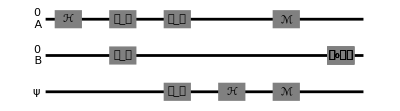

```mathematica
circ = QuantumCircuit[{h2, cn23,cn12, h1, m, cond}]
```

```mathematica
sNew = QuantumPartialTr[circ[s], {"ψ",  "0_A" }] [[1, "StateVector"]]//Normal 
{5/(2 √74),7/(2 √74)}
```